## 1. Topological charge

```mathematica
n={Cos[α[r,ϕ]] Sin[β[r,ϕ]],Sin[α[r,ϕ]] Sin[β[r,ϕ]],Cos[β[r,ϕ]]};
ddx=Cos[ϕ]D[n,r]-Sin[ϕ]/r D[n,ϕ];
ddy=Sin[ϕ]D[n,r]+Cos[ϕ]/r D[n,ϕ];
```

```mathematica
n.(ddx×ddy)//FullSimplify
```

```mathematica
Q=-1;
```

## 2. Classical hamiltonian

```mathematica
Npoints=400;
C1=1;(*exchange const*)
Dz=1;(*DM const*)
b=0.5;(*magnetic field const*)
An=0.1;(*Anisotropy const*)
tableB={};
err0=0.0001;
k1=0.5;
fromR0=2;
toR0=10;
```

```mathematica
R0=10
```

```mathematica
densEnergy=Table[
Setka=Table[N[R0/Npoints k],{k,1,Npoints}];
Setka=Prepend[Setka,err0];
beta=β/.NDSolve[{(Sin[β[r]] (An Cos[β[r]] r^2+b r^2+ C1 Cos[β[r]]-2 Dz r Sin[β[r]]))/r==C1 β'[r]+C1 r β''[r],β[err0]==π-√(b)err0,β[R0]==err0},β,{r,10^-5,R0},Method->{"Shooting", "StartingInitialConditions"->{β[err0]==π-√(b)k1 err0 , β'[err0] == -√(b) k1}} ]⟦1⟧;
wdens[r_]:=r (b(1-Cos[beta[r]])+An(1-(Cos[beta[r]])^2)+(Dz Cos[beta[r]] Sin[beta[r]])/r+(C1 Sin[beta[r]]^2)/(2 r^2)+Dz beta'[r]+1/2 C1 beta'[r]^2);
wdensTable=wdens[Setka];
W=2/(3 Npoints) Sum[ wdensTable⟦k-1⟧+4wdensTable⟦k⟧+wdensTable⟦k+1⟧,{k,2,Npoints,2}]/ R0;
{R0,W},{R0,fromR0,toR0,0.05}];
```

```mathematica
ListPlot[densEnergy,Joined->True]
R0=MinimalBy[densEnergy,Last][[1,1]]
```

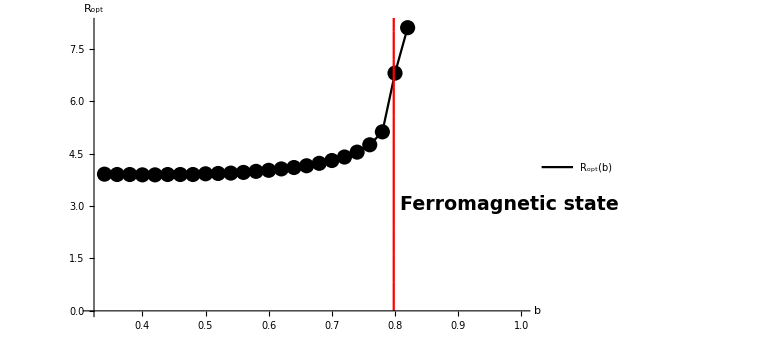

## 3. WKB derivate quantum hamiltonian:

```mathematica
An=0
SetAttributes[{Dz,Cex,M0,αo},Constant]
```

0

```mathematica
Uo1=({{Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ], -Cos[γ] Sin[α]-Cos[α] Cos[β] Sin[γ], Cos[α] Sin[β]}, {Cos[β] Cos[γ] Sin[α]+Cos[α] Sin[γ], Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ], Sin[α] Sin[β]}, {-Cos[γ] Sin[β], Sin[β] Sin[γ], Cos[β]}})/.{γ->M0  α};
```

```mathematica
X2=({{1/4 (-4 (Cos[γ]^2 Dt[β,x]^2+Dt[γ,x]^2)-Dt[α,x]^2 (3+Cos[2 β]-2 Cos[2 γ] Sin[β]^2)-8 Dt[α,x] (Cos[β] Dt[γ,x]+Cos[γ] Dt[β,x] Sin[β] Sin[γ])), -Cos[β] Dt[α,{x,2}]-Dt[γ,{x,2}]+Sin[γ] (Cos[γ] (Dt[β,x]^2-Dt[α,x]^2 Sin[β]^2)+2 Dt[α,x] Dt[β,x] Sin[β] Sin[γ]), Cos[γ] (Dt[β,{x,2}]-Cos[β] Dt[α,x]^2 Sin[β])+(2 Cos[β] Dt[α,x] Dt[β,x]+Dt[α,{x,2}] Sin[β]) Sin[γ]}, {Cos[β] Dt[α,{x,2}]+Dt[γ,{x,2}]+Cos[γ] (-2 Cos[γ] Dt[α,x] Dt[β,x] Sin[β]+(Dt[β,x]^2-Dt[α,x]^2 Sin[β]^2) Sin[γ]), 1/4 (-Dt[α,x]^2 (3+Cos[2 γ]+2 Cos[2 β] Sin[γ]^2)-4 (Dt[γ,x]^2+Dt[β,x]^2 Sin[γ]^2)+Dt[α,x] (-8 Cos[β] Dt[γ,x]+4 Dt[β,x] Sin[β] Sin[2 γ])), 2 Cos[β] Cos[γ] Dt[α,x] Dt[β,x]+Cos[γ] Dt[α,{x,2}] Sin[β]-Dt[β,{x,2}] Sin[γ]+Cos[β] Dt[α,x]^2 Sin[β] Sin[γ]}, {-Cos[γ] (Dt[β,{x,2}]+Dt[α,x] (Cos[β] Dt[α,x]+2 Dt[γ,x]) Sin[β])+(2 Dt[β,x] Dt[γ,x]-Dt[α,{x,2}] Sin[β]) Sin[γ], 2 Cos[γ] Dt[β,x] Dt[γ,x]-Cos[γ] Dt[α,{x,2}] Sin[β]+(Dt[β,{x,2}]+Dt[α,x] (Cos[β] Dt[α,x]+2 Dt[γ,x]) Sin[β]) Sin[γ], -Dt[β,x]^2-Dt[α,x]^2 Sin[β]^2}})/.{γ->M0 α};
```

```mathematica
X1={{0,-Cos[β] Dt[α,x]-Dt[γ,x],Cos[γ] Dt[β,x]+Dt[α,x] Sin[β] Sin[γ]},{Cos[β] Dt[α,x]+Dt[γ,x],0,Cos[γ] Dt[α,x] Sin[β]-Dt[β,x] Sin[γ]},{-Cos[γ] Dt[β,x]-Dt[α,x] Sin[β] Sin[γ],-Cos[γ] Dt[α,x] Sin[β]+Dt[β,x] Sin[γ],0}}/.{γ->M0  α};
delrot={Dt[β,r[1]]->  Cos[ϕ]Dt[β,r]-Sin[ϕ]/r  Dt[β,ϕ], 
Dt[α,r[1]]->  Cos[ϕ]Dt[α,r]-Sin[ϕ]/r  Dt[α,ϕ],
Dt[β,r[2]]->Sin[ϕ]Dt[β,r]+Cos[ϕ]/r  Dt[β,ϕ],
Dt[α,r[2]]->Sin[ϕ]Dt[α,r]+Cos[ϕ]/r  Dt[α,ϕ] };
```

```mathematica
χ1=s Sum[(r[l]X1/.x->r[l]),{l,1,2}]/.delrot/.{r[1]->r1 Cos[ϕ1],r[2]->r1 Sin[ϕ1]}/.{Dt[α,r]->0,Dt[α,ϕ]->1,Dt[β,ϕ]->0 }/.{α->ϕ+αo,β->β[r]}//FullSimplify;
ex={β'[r]->D[2 ArcTan[1/r],r]//FullSimplify, β[r]->2 ArcTan[1/r]};
```

```mathematica
S1={(√(2s))/2(ap+a),-ⅈ(√(2s))/2(a-ap),s-ap a};
S2={(√s (a+ap))/(√2),-(ⅈ √s (a-ap))/(√2),-ap a};
```

```mathematica
DMi1=Table[-Dz Sum[Signature[{i,k,l}](X1⟦k,j⟧/.{x->r[m]})Uo1⟦m,l⟧,{k,3},{m,2},{l,3}],{i,3},{j,3}]//Simplify;
```

```mathematica
Unew=Dt[Uo1,x];
```

```mathematica
DMi2=Table[Dz Sum[Signature[{a,b,c}](Unew⟦e,c⟧/.{x->r[e]}),{c,3},{e,2}],{a,3},{b,3}]//Simplify;
```

```mathematica
DM1=DMi1/.delrot/.{Dt[α,r]->0,Dt[α,ϕ]->1,Dt[β,ϕ]->0 }/.{β->β[r]}/.{α->ϕ+αo}//FullSimplify;
```

```mathematica
DM2=DMi2/.delrot/.{Dt[α,r]->0,Dt[α,ϕ]->1,Dt[β,ϕ]->0 }/.{β->β[r]}/.{α->ϕ+αo}//FullSimplify;
```

```mathematica
Sa={1/2 √(2 s) (a+ap),1/2 (-ⅈ) √(2 s) (a-ap),s-ap a};

Sdt=FullSimplify[Dt[Sa,x]/.Dt[s,x]->0];
Dt[Sa,x];
UU=Uo1;
US=Table[Sum[UU[[e,c]](Sdt[[b]]/.{x->r[e]}),{e,2}],{c,3},{b,3}]/.{
Dt[a,r[1]]->  Cos[ϕ]Dt[a,r]-Sin[ϕ]/r  Dt[a,ϕ], 
Dt[ap,r[1]]->  Cos[ϕ]Dt[ap,r]-Sin[ϕ]/r  Dt[ap,ϕ],
Dt[a,r[2]]->Sin[ϕ]Dt[a,r]+Cos[ϕ]/r  Dt[a,ϕ],
Dt[ap,r[2]]->Sin[ϕ]Dt[ap,r]+Cos[ϕ]/r  Dt[ap,ϕ] }//FullSimplify;
GradCoef1=(-Dz Sum[Signature[{i,k,l}]Sa[[i]]US[[l,k]],{i,3},{k,3},{l,3}])/.{α->ϕ+αo,β->β[r]};
```

```mathematica
GradCoef2=(-Cex( (Sum[Sa[[k]](X1[[k,i]]/.{ x->r[e]})(Sdt[[i]]/.{x->r[e]}),{e,2},{k,3},{i,3}])/.{
Dt[a,r[1]]->  Cos[ϕ]Dt[a,r]-Sin[ϕ]/r  Dt[a,ϕ], 
Dt[ap,r[1]]->  Cos[ϕ]Dt[ap,r]-Sin[ϕ]/r  Dt[ap,ϕ],
Dt[a,r[2]]->Sin[ϕ]Dt[a,r]+Cos[ϕ]/r  Dt[a,ϕ],
Dt[ap,r[2]]->Sin[ϕ]Dt[ap,r]+Cos[ϕ]/r  Dt[ap,ϕ]}/.{delrot}))/.{α->ϕ+αo,β->β[r]};
```

```mathematica
GradCoef1parts=-Dz (Sum[Signature[{i,k,l}]S2[[i]]US[[l,k]],{i,3},{k,3},{l,3}])/.{α->ϕ+αo,β->β[r]};
```

```mathematica
GradCoef2parts=Cex( (Sum[(Sdt[[k]]/.{x->r[e]})(X1[[k,i]]/.{x->r[e]})S2[[i]],{e,2},{k,3},{i,3}])/.{
Dt[a,r[1]]->  Cos[ϕ]Dt[a,r]-Sin[ϕ]/r  Dt[a,ϕ], 
Dt[ap,r[1]]->  Cos[ϕ]Dt[ap,r]-Sin[ϕ]/r  Dt[ap,ϕ],
Dt[a,r[2]]->Sin[ϕ]Dt[a,r]+Cos[ϕ]/r  Dt[a,ϕ],
Dt[ap,r[2]]->Sin[ϕ]Dt[ap,r]+Cos[ϕ]/r  Dt[ap,ϕ]}/.{delrot})/.{α->ϕ+αo,β->β[r]};
```

```mathematica
Grad3=-Cex/2 S1.Dt[S1,{x,2}]/.{Dt[a,{x,2}]->Δa,Dt[ap,{x,2}]->Δap,Dt[ap,x]->∇ap,Dt[a,x]->∇a , Dt[s,x]->0,  Dt[s,{x,2}]->0};
```

```mathematica
Hex1=-Cex/2(X2/.{Dt[β,x]->∇β,Dt[α,x]-> ∇α, Dt[α,{x,2}]-> Δα, Dt[β,{x,2}]-> Δβ}//Expand)/. {Δα->0,∇α ∇β->0,(∇α)^2->1/r^2}//Simplify;
```

```mathematica
Hex2tmp1=Cex Dt[X1,x]//FullSimplify;
Hex2tmp2=Hex2tmp1/.{Dt[β,x]->∇β,Dt[α,x]-> ∇α, Dt[α,{x,2}]-> Δα, Dt[β,{x,2}]-> Δβ}//Expand;
Hex2=Hex2tmp2//.{Δα->0,∇α ∇β->0,(∇α)^2->1/r^2};
```

```mathematica
U1=(Hex1/.{ Δβ->Dt[β,{r,2}]+Dt[β,r]/r,∇β->Dt[β,r]})/.{β->β[r], α->ϕ+αo}//FullSimplify;
U2=(Hex2/.{ Δβ->Dt[β,{r,2}]+Dt[β,r]/r,∇β->Dt[β,r]})/.{β->β[r], α->ϕ+αo}//FullSimplify;
Uo=Uo1/.{α->ϕ+αo,β->β[r]};


X=U1⟦1,3⟧+DM1⟦1,3⟧-b /2Uo⟦3,1⟧+ⅈ(U1⟦2,3⟧+DM1⟦2,3⟧-b/2 Uo⟦3,2⟧)/.{αo->π/2, Dt[ϕ,r]->0};
```

```mathematica
ddbeta2=(Solve[X==0,β''[r]]//FullSimplify)[[1]];
```

```mathematica
HamiltDMI=(Grad3+GradCoef1+GradCoef2+S1.U1.S1+S1.DM1.S1- b s Uo[[3]].S1- An  (Uo[[3]].S1)^2)/.ddbeta2/.{αo->π/2, Dt[ϕ,r]->0};
```

```mathematica
Coefficient[HamiltDMI, s^2]//Expand
```

{-b Cos[β[r]]+(Dz Cos[β[r]] Sin[β[r]])/r+(Cex Sin[β[r]]^2)/(2 r^2)+Dz β'[r]+1/2 Cex β'[r]^2}

Now s^3/2 not 0 but after integration by parts hamiltonian become equal to 0:

```mathematica
HamilByParts=(Grad3+GradCoef1parts+GradCoef2parts+S1.U1.S1+S1.DM1.S1+S1.U2.S2+S1.DM2.S2- b s Uo[[3]].S1- An  (Uo[[3]].S1)^2 )/.{β''[r]->1/(Cex r^2)(b r^2 Sin[β[r]]+Cex Cos[β[r]] Sin[β[r]]+2 An r^2 Cos[β[r]] Sin[β[r]]-2 Dz r Sin[β[r]]^2-Cex r β'[r])}/.{αo->π/2};
Coefficient[HamilByParts, s^(3/2)]/.{Dt[a,ϕ]-> ⅈ m a, Dt[ap,ϕ]->-ⅈ m ap}//FullSimplify
```

{0}

```mathematica
H=Coefficient[HamiltDMI, s]/.{ Dt[a,ϕ]->-ⅈ Lz a, Dt[ap,ϕ]-> ⅈ Lz ap}//Expand;
```

```mathematica
(H/.{ap->SuperDagger[a]})//FullSimplify
```

```mathematica
{1/(8 r^2)(8 Cex r^2 ∇a ∇SuperDagger[a]+2 a SuperDagger[a] (Cex-8 Cex Lz M0+4 Cex M0^2+3 Cex Cos[2 β[r]]+8 Dz (Lz-M0) r Sin[β[r]]+4 Cos[β[r]] (2 Cex (-Lz+M0)+b r^2-3 Dz r Sin[β[r]])-2 r^2 β'[r] (2 Dz+Cex β'[r]))-2 ⅇ^(-ⅈ M0 (π+2 ϕ)) (SuperDagger[a])^2 (Cex Sin[β[r]]^2+Dz r Sin[2 β[r]]-r^2 β'[r] (2 Dz+Cex β'[r]))+a^2 ⅇ^(ⅈ M0 (π+2 ϕ)) (-2 Sin[β[r]] (2 Dz r Cos[β[r]]+Cex Sin[β[r]])+2 r^2 β'[r] (2 Dz+Cex β'[r])))}
```

```mathematica
aaplus=Coefficient[(H/.{ap->SuperDagger[a]}), SuperDagger[a] SuperDagger[a]] SuperDagger[a] SuperDagger[a]//FullSimplify//Expand

aa=Coefficient[(H/.{ap->SuperDagger[a]}), a a]a a //FullSimplify//Expand

(H/.{ap->SuperDagger[a]})- aa -aaplus//FullSimplify//Expand
```

{-(Dz ⅇ^(-ⅈ M0 (π+2 ϕ)) Cos[β[r]] Sin[β[r]] (a^†)^2)/(2 r)-(Cex ⅇ^(-ⅈ M0 (π+2 ϕ)) Sin[β[r]]^2 (a^†)^2)/(4 r^2)+1/2 Dz ⅇ^(-ⅈ M0 (π+2 ϕ)) (a^†)^2 β'[r]+1/4 Cex ⅇ^(-ⅈ M0 (π+2 ϕ)) (a^†)^2 β'[r]^2}

{-(a^2 Dz ⅇ^(ⅈ M0 (π+2 ϕ)) Cos[β[r]] Sin[β[r]])/(2 r)-(a^2 Cex ⅇ^(ⅈ M0 (π+2 ϕ)) Sin[β[r]]^2)/(4 r^2)+1/2 a^2 Dz ⅇ^(ⅈ M0 (π+2 ϕ)) β'[r]+1/4 a^2 Cex ⅇ^(ⅈ M0 (π+2 ϕ)) β'[r]^2}

{Cex ∇a ∇a^†+(a Cex a^†)/(4 r^2)-(2 a Cex Lz M0 a^†)/r^2+(a Cex M0^2 a^†)/r^2+a b Cos[β[r]] a^†-(2 a Cex Lz Cos[β[r]] a^†)/r^2+(2 a Cex M0 Cos[β[r]] a^†)/r^2+(3 a Cex Cos[2 β[r]] a^†)/(4 r^2)+(2 a Dz Lz Sin[β[r]] a^†)/r-(2 a Dz M0 Sin[β[r]] a^†)/r-(3 a Dz Cos[β[r]] Sin[β[r]] a^†)/r-a Dz a^† β'[r]-1/2 a Cex a^† β'[r]^2}

```mathematica
aaplus/.{SuperDagger[a]->ⅇ^(ⅈ ϕ)SuperDagger[a],a->ⅇ^(-ⅈ ϕ)a}//Expand
aa/.{SuperDagger[a]->ⅇ^(ⅈ ϕ)SuperDagger[a],a->ⅇ^(-ⅈ ϕ)a}//Expand
(((H)/.{ap->SuperDagger[a]}/.{Lz->1+Lz})+2a Cex Lz/r^2 SuperDagger[a]+a Cex 1/r^2 SuperDagger[a]- aa -aaplus//FullSimplify)//Expand
```

## 4. Const:

```mathematica
err0=0.0001;
k1=0.6;
maxMode=4; (*Magnet quantum number m*)
Nsize=180; (*Size of matrix*)
Npoints=600;
C1=1;(*C*)
b=0.6; (*Magnetic field*)
Dz=1; (*Dzyaloshiskiy-Morya interaction const*)
An=0; (*Anisotropy const*)
m=1;
fromR0=3;
toR0=6;
densEnergy=Table[
Setka=Table[N[R0/Npoints k],{k,1,Npoints}];
Setka=Prepend[Setka,err0];
beta=β/.NDSolve[{(Sin[β[r]] (2An Cos[β[r]] r^2+b r^2+ C1 Cos[β[r]]-2 Dz r Sin[β[r]]))/r==C1 β'[r]+C1 r β''[r],β[err0]==π-√(b)err0,β[R0]==err0},β,{r,10^-5,R0},Method->{"Shooting", "StartingInitialConditions"->{β[err0]==π-√(b)k1 err0 , β'[err0] == -√(b) k1}} ]⟦1⟧;
wdens[r_]:=r (b(1-Cos[beta[r]])+An(1-(Cos[beta[r]])^2)+(Dz Cos[beta[r]] Sin[beta[r]])/r+(C1 Sin[beta[r]]^2)/(2 r^2)+Dz beta'[r]+1/2 C1 beta'[r]^2);
wdensTable=wdens[Setka];
W=2/(3 Npoints) Sum[ wdensTable⟦k-1⟧+4wdensTable⟦k⟧+wdensTable⟦k+1⟧,{k,2,Npoints,2}]/ R0;
{R0,W},{R0,fromR0,toR0,0.05}];
R0=MinimalBy[densEnergy,Last][[1,1]]
a0=Sqrt[π/2]R0/3^(1/4);
BZ=Table[N[BesselJZero[m,k],7],{m,0,maxMode},{k,1,Nsize}];
dBZ[n_,j_]:=If[n≠0 ,x/.FindRoot[(BesselJ[-1+n,x]-BesselJ[1+n,x])==0,{x,(If[j>1,BesselJZero[n,j-1],1.8]+BesselJZero[n,j])/2,If[j>1,BesselJZero[n,j-1],1.8],BesselJZero[n,j]}],N[BesselJZero[n+1,j]]];
zeros=Table[dBZ[m,k],{m,0,maxMode},{k,1,Nsize}];
```

4.

## 5. Algorithm (case β(R_0)=0):

```mathematica
Setka=Table[err0 KroneckerDelta[0,k]+R0/Npoints k,{k,0,Npoints}];

λn[n_,m_]:=(BZ⟦Abs[m]+1⟧⟦n⟧/R0)^2;
ϕn[n_,r_,m_]:=Sqrt[2]/Abs[R0 ((D[BesselJ[m,rr1],rr1])/.rr1->BZ⟦Abs[m]+1⟧⟦n⟧) ]BesselJ[m,BZ⟦Abs[m]+1⟧⟦n⟧ /R0  r];

λn1[n_]:=λn[n,m+1];
ϕn1[n_,r_]:=ϕn[n,r,m+1];

λn2[n_]:=λn[n,m-1];
ϕn2[n_,r_]:=ϕn[n,r,m-1];


matrxϕn1=Parallelize[Table[ϕn1[k,Setka],{k,1,Nsize}]];
matrxϕn2=Parallelize[Table[ϕn2[k,Setka],{k,1,Nsize}]];

beta=β/.NDSolve[{(Sin[β[r]] (2An Cos[β[r]] r^2+b r^2+C1 Cos[β[r]]-2 Dz r Sin[β[r]]))/r==C1 β'[r]+r C1 β''[r],β[err0]==π-√(b)err0,β[R0]==err0},β,{r,10^-5,R0},Method->{"Shooting", "StartingInitialConditions"->{β[err0]==π-√(b)k1 err0 , β'[err0] == -√(b)k1 }} ]⟦1⟧;

βmin[r_]:=beta[r];
dβmin[r_]:=beta'[r];
funcV0[r_]:=r(1/2 An(1+3Cos[2βmin[r]])+ b Cos[βmin[r]]+(3 C1 (Cos[2 βmin[r]]-1))/(4 r^2)-(3 Dz Cos[βmin[r]] Sin[βmin[r]])/r-Dz dβmin[r]-1/2 C1( dβmin[r])^2);
funcV1[r_]:=r(-(2 C1 (Cos[βmin[r]]+1))/r^2+(2 Dz Sin[βmin[r]])/r);
funcG[r_]:=r(1/2 An  (Sin[βmin[r]])^2+(C1 Sin[βmin[r]]^2)/(2 r^2)+(Dz Sin[2βmin[r]])/(2 r)-Dz dβmin[r]-1/2 C1 (dβmin[r])^2);


pointsFuncV0=funcV0[Setka];
pointsFuncV1=funcV1[Setka];
pointsFuncG=funcG[Setka];

(*It's Simpson's rule*)

 F1[k1_,k2_]:=KroneckerDelta [k1 ,k2 ]C1 λn1[k1]+R0/(3 Npoints) Sum[ matrxϕn1⟦k1,k-1⟧
matrxϕn1⟦k2,k-1⟧(pointsFuncV0⟦k-1⟧+m pointsFuncV1⟦k-1⟧)+
4matrxϕn1⟦k1,k⟧matrxϕn1⟦k2,k⟧(pointsFuncV0⟦k⟧+m pointsFuncV1⟦k⟧)+
matrxϕn1⟦k1,k+1⟧matrxϕn1⟦k2,k+1⟧(pointsFuncV0⟦k+1⟧+m pointsFuncV1⟦k+1⟧),{k,2,Npoints,2}];

 F2[k1_,k2_]:=KroneckerDelta [k1 ,k2 ]C1 λn2[k1]+R0/(3 Npoints) Sum[ matrxϕn2⟦k1,k-1⟧
matrxϕn2⟦k2,k-1⟧(pointsFuncV0⟦k-1⟧-m pointsFuncV1⟦k-1⟧)+4matrxϕn2⟦k1,k⟧
matrxϕn2⟦k2,k⟧(pointsFuncV0⟦k⟧-m pointsFuncV1⟦k⟧)+matrxϕn2⟦k1,k+1⟧
matrxϕn2⟦k2,k+1⟧(pointsFuncV0⟦k+1⟧-m pointsFuncV1⟦k+1⟧),{k,2,Npoints,2}];

 G[k1_,k2_]:=R0/(3 Npoints) Sum[ 
matrxϕn1⟦k1,k-1⟧matrxϕn2⟦k2,k-1⟧pointsFuncG⟦k-1⟧+
4matrxϕn1⟦k1,k⟧matrxϕn2⟦k2,k⟧pointsFuncG⟦k⟧+
matrxϕn1⟦k1,k+1⟧matrxϕn2⟦k2,k+1⟧pointsFuncG⟦k+1⟧,{k,2,Npoints,2}];

     F1table=Table[If[i<=j,F1[i,j],0],{i,1,Nsize},{j,1,Nsize}];
For[i=1,i≤Nsize,i++,
(For[k=1,k≤Nsize,k++,F1table⟦k,i⟧=F1table⟦i,k⟧])
];

     F2table=Table[If[i<=j,F2[i,j],0],{i,1,Nsize},{j,1,Nsize}];
For[i=1,i≤Nsize,i++,
(For[k=1,k≤Nsize,k++,F2table⟦k,i⟧=F2table⟦i,k⟧])
];

 Gtable=Table[G[i,j],{i,1,Nsize},{j,1,Nsize}];

matrixHdG=ArrayFlatten[{{F1table, Gtable}, {-Transpose[Gtable], -F2table}}];
matrixHdG2=matrixHdG⟦1;;2(Nsize-10),1;;2(Nsize-10)⟧;

moda0=Eigenvalues[matrixHdG];
tmpmoda=Eigenvalues[matrixHdG2];

Do[If[Im[Chop[moda0⟦i⟧]]>err0,Print["There is a complex value! R_0=",R0,", E[",i,"]=",moda0⟦i⟧] ],{i,1,2 Nsize}];

If[Length[Select[moda0,#>0&]]==Length[Select[moda0,#<0&]],Print["Number of positive values equals to number of negative ones"],Print["Alarm!!! Number of positive values NOT equals to number of negative ones"]];

mPositive=Sort[Select[moda0,#>0&],Abs[#1]<Abs[#2]&];
mNegative=Sort[Select[moda0,#<0&],Abs[#1]<Abs[#2]&];
tmpPos=Sort[Select[tmpmoda,#>0&],Abs[#1]<Abs[#2]&];
tmpNeg=Sort[Select[tmpmoda,#<0&],Abs[#1]<Abs[#2]&];

Print["m is ", m];
Print["Error=",(R0/(2Npoints))^2+Max[Table[Abs[tmpPos⟦k⟧-mPositive⟦k⟧],{k,1,10}]]] ;
Print["Energy for modes "];
Print[mPositive⟦1;;8⟧,  " m = ", m];
Print[Abs[mNegative⟦1;;8⟧ ], " m = ", -m];
Print["R_0 is ", R0];
If[m≠0,QuantumCorrections=Sum[Abs[moda0⟦i⟧],{i,1,2Nsize}]-Sum[F1table⟦i,i⟧ +F2table⟦i,i⟧ ,{i,1,Nsize}],
QuantumCorrections=0.5 (Sum[Abs[moda0⟦i⟧],{i,1,2Nsize}]-Sum[F1table⟦i,i⟧ +F2table⟦i,i⟧ ,{i,1,Nsize}])];
Print["Eqc = ", QuantumCorrections]
```

Number of positive values equals to number of negative ones

m is 1

Error=0.0000111111

Energy for modes

{1.86219,5.04447,9.22255,14.5238,21.0281,28.7541,37.7079,47.8922} m = 1

{0.122193,2.12719,4.89877,8.91026,14.1548,20.6327,28.3439,37.2887} m = -1

R_0 is 4.

Eqc = -0.526459

## 6. Lattice:

```mathematica
{eigvlH,eigvecH}=Eigensystem[matrixHdG];
eigvecH[[2Nsize]];
V=Transpose[Inverse[eigvecH]];
Vt=Transpose[eigvecH];
τzz1=DiagonalMatrix[Table[1,{n,1,Nsize}]];
τzz=ArrayFlatten[{{τzz1, 0}, {0, -τzz1}}];
Chop[V.matrixHdG.Vt]//MatrixForm;
```

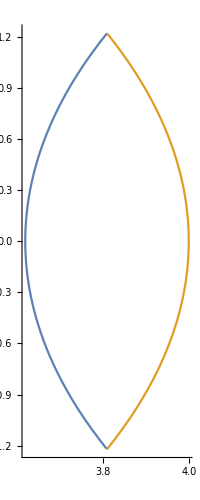

0.623843

0.623843

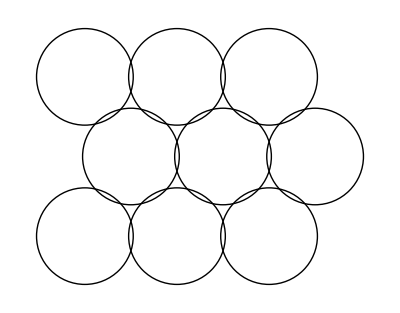

```mathematica
ϕ0=0;
PolarPlot[{-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕ-2 ϕ0])+2 a0 Cos[ϕ-ϕ0],R0},{ϕ,ϕ0-ArcCos[a0/R0],ϕ0+ArcCos[a0/R0]}]
LinsSq=NIntegrate[Integrate[r,{r,-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕ-2 ϕ0])+2 a0 Cos[ϕ-ϕ0],R0}],{ϕ,ϕ0-ArcCos[a0/R0],ϕ0+ArcCos[a0/R0]}]
2(-R0^2 Cos[ArcCos[a0/R0]]Sin[ArcCos[a0/R0]]+R0^2 ArcCos[a0/R0])
Graphics[Table[Circle[{i+((-1)^j+1)/4,Sqrt[3]/2j}, R0/(2a0)  (*3^(1/4)/(√(2 π))*) ],{i,3},{j,3}]]
```

```mathematica
pnt[x0_]:=
Module[{k=1},
min1=Abs[x0-Setka⟦k⟧];
Do[If[Abs[x0-Setka⟦k1⟧]<Abs[x0-Setka⟦k⟧],k=k1;],{k1,1,Npoints+1}];
k
];
hϕ=ArcCos[a0/R0]/40;
ϕ1[r_,ϕ_]:=-ArcSin[r Sin[ϕ-ϕ0]/Sqrt[r^2+4 a0^2-4 a0 r Cos[ϕ-ϕ0]]]+Pi+ϕ0;
r1[r_,ϕ_]:=Sqrt[r^2+4 a0^2-4a0 r Cos[ϕ-ϕ0]];
ϕtable =Table[ϕ,{ϕ,ϕ0-ArcCos[a0/R0] ,ϕ0+ArcCos[a0/R0],hϕ}];
pntTable=Table[{ϕ,Table[pnt[r1[Setka⟦k⟧,ϕ]],{k,1,Npoints+1}]},{ϕ,ϕ0-ArcCos[a0/R0] ,ϕ0+ArcCos[a0/R0],hϕ}];
```

```mathematica
exchRadialF1[k1_,k2_,kt_]:=R0/(3 (Npoints))Sum[
ⅇ^(ⅈ (m) ϕ1[Setka⟦k-1⟧,ϕtable⟦kt⟧]) matrxϕn1⟦k1,k-1⟧matrxϕn1⟦k2,pntTable⟦kt⟧⟦2⟧⟦k-1⟧⟧(C1 λn1[k1]Setka⟦k-1⟧+pointsFuncV0⟦k-1⟧+m pointsFuncV1⟦k-1⟧)+

4 ⅇ^(ⅈ  (m) ϕ1[Setka⟦k⟧,ϕtable⟦kt⟧])matrxϕn1⟦k1,k⟧matrxϕn1⟦k2,pntTable⟦kt⟧⟦2⟧⟦k⟧⟧(C1 λn1[k1]Setka⟦k⟧+pointsFuncV0⟦k⟧+m pointsFuncV1⟦k⟧)+

ⅇ^(ⅈ (m) ϕ1[Setka⟦k+1⟧,ϕtable⟦kt⟧])matrxϕn1⟦k1,k+1⟧matrxϕn1⟦k2,pntTable⟦kt⟧⟦2⟧⟦k+1⟧⟧(C1 λn1[k1]Setka⟦k+1⟧+pointsFuncV0⟦k+1⟧+m pointsFuncV1⟦k+1⟧),

{k,pnt[-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕtable⟦kt⟧-2 ϕ0])+2 a0 Cos[ϕtable⟦kt⟧-ϕ0]],Npoints,2}];


exchRadialF2[k1_,k2_,kt_]:=
R0/(3 (Npoints))Sum[
ⅇ^(ⅈ  (m) ϕ1[Setka⟦k-1⟧,ϕtable⟦kt⟧]) matrxϕn2⟦k1,k-1⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k-1⟧⟧(C1 λn2[k1]Setka⟦k-1⟧+pointsFuncV0⟦k-1⟧-m pointsFuncV1⟦k-1⟧)+

4 ⅇ^(ⅈ  (m) ϕ1[Setka⟦k⟧,ϕtable⟦kt⟧])matrxϕn2⟦k1,k⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k⟧⟧(C1 λn2[k1]Setka⟦k⟧+pointsFuncV0⟦k⟧-m pointsFuncV1⟦k⟧)+

ⅇ^(ⅈ  (m) ϕ1[Setka⟦k+1⟧,ϕtable⟦kt⟧])matrxϕn2⟦k1,k+1⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k+1⟧⟧(C1 λn2[k1]Setka⟦k+1⟧+pointsFuncV0⟦k+1⟧-m pointsFuncV1⟦k+1⟧),

{k,pnt[-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕtable⟦kt⟧-2 ϕ0])+2 a0 Cos[ϕtable⟦kt⟧-ϕ0]],Npoints,2}];

exchRadialG[k1_,k2_,kt_]:=R0/(3 Npoints)Sum[
ⅇ^(ⅈ (m) ϕ1[Setka⟦k-1⟧,ϕtable⟦kt⟧]) matrxϕn1⟦k1,k-1⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k-1⟧⟧pointsFuncG⟦k-1⟧+
4 ⅇ^(ⅈ  (m) ϕ1[Setka⟦k⟧,ϕtable⟦kt⟧])matrxϕn1⟦k1,k⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k⟧⟧pointsFuncG⟦k⟧+
ⅇ^(ⅈ  (m)ϕ1[Setka⟦k+1⟧,ϕtable⟦kt⟧])matrxϕn1⟦k1,k+1⟧matrxϕn2⟦k2,pntTable⟦kt⟧⟦2⟧⟦k+1⟧⟧pointsFuncG⟦k+1⟧,{k,pnt[-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕtable⟦kt⟧-2 ϕ0])+2 a0 Cos[ϕtable⟦kt⟧-ϕ0]],Npoints,2}];

exchF1[k1_,k2_]:=
Chop[hϕ Sum[ⅇ^(-ⅈ  (m) ϕtable⟦j⟧)exchRadialF1[k1,k2,j],{j,1,Length[ϕtable] }]];

exchF2[k1_,k2_]:=
 Chop[hϕ Sum[ⅇ^(-ⅈ  (m) ϕtable⟦j⟧)exchRadialF2[k1,k2,j],{j,1,Length[ϕtable] }]];

exchG[k1_,k2_]:=
Chop[hϕ Sum[ⅇ^(-ⅈ  (m) ϕtable⟦j⟧) exchRadialG[k1,k2,j],{j,1,Length[ϕtable] }]];

thetaFunc[x_,y_]:=If[(x^2+y^2≤R0^2)&&((x-2 a0)^2+y^2≤R0^2),1,0];

exchFF1[k1_,k2_,ϕ0_]:=NIntegrate[ⅇ^(-ⅈ (m) ϕ)
NIntegrate[
(
C1 λn1[k1]r ϕn1[k1,r]
+(funcV0[r]+m funcV1[r])ϕn1[k1,r]
)
ⅇ^(ⅈ (m )ϕ1[r,ϕ])ϕn1[k2,r1[r,ϕ]],{r,-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕ-2 ϕ0])+2 a0 Cos[ϕ-ϕ0],R0}],{ϕ,ϕ0-ArcCos[a0/R0],ϕ0+ArcCos[a0/R0]}]
exchFF2[k1_,k2_,ϕ0_]:=NIntegrate[ⅇ^(-ⅈ (m-1) ϕ)
NIntegrate[
(C1 λn2[k1]r ϕn2[k1,r]+(funcV0[r]-m funcV1[r])ϕn2[k1,r])
ⅇ^(ⅈ (m )ϕ1[r,ϕ])ϕn2[k2,r1[r,ϕ]],{r,-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕ-2 ϕ0])+2 a0 Cos[ϕ-ϕ0],R0}],{ϕ,ϕ0-ArcCos[a0/R0],ϕ0+ArcCos[a0/R0]}]

exchGG[k1_,k2_,ϕ0_]:=NIntegrate[
NIntegrate[
ⅇ^(-ⅈ (m) ϕ)ϕn1[k1,r]funcG[r] ⅇ^(ⅈ (m -1)ϕ1[r,ϕ])ϕn2[k2,r1[r,ϕ]],{r,-√(-2 a0^2+R0^2+2 a0^2 Cos[2 ϕ-2 ϕ0])+2 a0 Cos[ϕ-ϕ0],R0}],{ϕ,ϕ0-ArcCos[a0/R0],ϕ0+ArcCos[a0/R0]}]
exchF1Exact[k1_,k2_]:=NIntegrate[
ⅇ^(-ⅈ  (m) ArcTan[y/x])ⅇ^(ⅈ  (m+1)(-ArcTan[y/(2 a0-x)]))
 ϕn1[k1,√(x^2+y^2)] ϕn1[k2,√((x-2 a0)^2+y^2)]( C1 λn1[k1]+(funcV0[√(x^2+y^2)]+m funcV1[√(x^2+y^2)])/√(x^2+y^2)) thetaFunc[x,y],{x,0,R0},{y,-R0,R0}];

exchF2Exact[k1_,k2_]:=NIntegrate[ⅇ^(-ⅈ  (m)ArcTan[y/x])ⅇ^(ⅈ  (m) (-ArcTan[y/(2 a0-x)]))  ϕn2[k1,√(x^2+y^2)] ϕn2[k2,√((x-2 a0)^2+y^2)]( C1 λn2[k1]+(funcV0[√(x^2+y^2)]-m funcV1[√(x^2+y^2)])/√(x^2+y^2)) thetaFunc[x,y],{x,0,R0},{y,-R0,R0}];

exchGExact[k1_,k2_]:=NIntegrate[ⅇ^(-ⅈ  (m) ArcTan[y/x])ⅇ^(ⅈ (m) (-ArcTan[y/(2 a0-x)]))ϕn1[k1,√(x^2+y^2)]ϕn2[k2,√((x-2 a0)^2+y^2)]  (funcG[√(x^2+y^2)]/√(x^2+y^2)) thetaFunc[x,y],{x,0,R0},{y,-R0,R0}];
```

```mathematica
exchF1t=Parallelize[Table[exchF1[i,j],{i,1,Nsize},{j,1,Nsize}]];
exchF2t=Parallelize[Table[exchF2[i,j],{i,1,Nsize},{j,1,Nsize}]];
exchGt=Parallelize[Table[exchG[i,j],{i,1,Nsize},{j,1,Nsize}]];
```

```mathematica
matrixExch=ArrayFlatten[{{exchF1t, exchGt}, {-Transpose[exchGt], -exchF2t}}];
```

```mathematica
vecZeroMode1=eigvecH[[2Nsize]];
E01=vecZeroMode1.matrixHdG.vecZeroMode1;
(*Sum[If[eigvecH[[k]].matrixHdG.eigvecH[[k]]<0,vecZeroMode1.matrixExch.eigvecH[[k]],0],{k,1,2Nsize}]*)

Et1=vecZeroMode1.matrixExch.vecZeroMode1
Table[{2(Nsize-kkkk),vecZeroMode1⟦1;;2(Nsize-kkkk)⟧.matrixExch⟦1;;2(Nsize-kkkk),1;;2(Nsize-kkkk)⟧.vecZeroMode1⟦1;;2(Nsize-kkkk)⟧},{kkkk,Nsize-2,0,-2}]
mode1[kx_,ky_]:=-(E01+2( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])Et1);
```

0.0000350983

{{4,-0.0000326161},{8,-0.0000316503},{12,-0.0000307323},{16,-0.0000304279},{20,-0.0000303068},{24,-0.0000302544},{28,-0.0000302284},{32,-0.0000302132},{36,-0.0000302034},{40,-0.0000301968},{44,-0.0000301925},{48,-0.0000301895},{52,-0.0000301874},{56,-0.0000301858},{60,-0.0000301846},{64,-0.0000301837},{68,-0.000030183},{72,-0.0000301824},{76,-0.000030182},{80,-0.0000301816},{84,-0.0000301813},{88,-0.000030181},{92,-0.0000301808},{96,-0.0000301806},{100,-0.0000301805},{104,-0.0000301804},{108,-0.0000301803},{112,-0.0000301802},{116,-0.0000301801},{120,-0.00003018},{124,-0.00003018},{128,-0.0000301799},{132,-0.0000301799},{136,-0.0000301798},{140,-0.0000301798},{144,-0.0000301798},{148,-0.0000301797},{152,-0.0000301797},{156,-0.0000301797},{160,-0.0000301797},{164,-0.0000301796},{168,-0.0000301796},{172,-0.0000301796},{176,-0.0000301796},{180,-0.0000301796},{184,-0.0000483082},{188,0.0000395521},{192,0.0000374369},{196,0.0000361356},{200,0.0000356148},{204,0.0000353933},{208,0.0000352872},{212,0.0000352273},{216,0.0000351891},{220,0.0000351637},{224,0.0000351469},{228,0.0000351355},{232,0.0000351275},{236,0.0000351215},{240,0.0000351169},{244,0.0000351134},{248,0.0000351108},{252,0.0000351087},{256,0.000035107},{260,0.0000351056},{264,0.0000351045},{268,0.0000351036},{272,0.0000351028},{276,0.0000351022},{280,0.0000351016},{284,0.0000351012},{288,0.0000351008},{292,0.0000351004},{296,0.0000351002},{300,0.0000350999},{304,0.0000350997},{308,0.0000350995},{312,0.0000350993},{316,0.0000350992},{320,0.0000350991},{324,0.0000350989},{328,0.0000350988},{332,0.0000350988},{336,0.0000350987},{340,0.0000350986},{344,0.0000350985},{348,0.0000350985},{352,0.0000350984},{356,0.0000350984},{360,0.0000350983}}

```mathematica
(*vecZeroMode2=eigvecH[[2Nsize]];
E02=vecZeroMode2.matrixHdG.vecZeroMode2
Et2=vecZeroMode2.matrixExch.vecZeroMode2
mode2[kx_,ky_]:=-(3/4E02+2/4( Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])Et2);
mode2[0,0]*)
```

-Graphics3D-

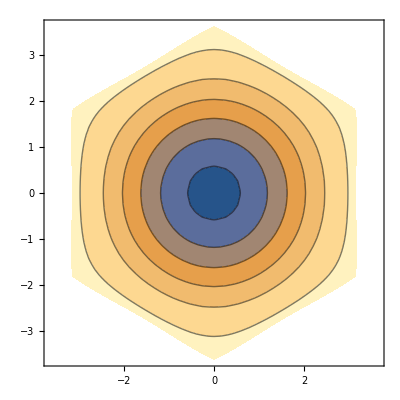

```mathematica
RRR=2π/√3;
Hexagone=Interpolation[Table[{a,RRR {Cos[a],Sin[a]}},{a,-π,π,π/3}],InterpolationOrder->1];
Plot3D[{mode1[x,y],mode2[x,y]},{x,-RRR,RRR},{y,-RRR,RRR},RegionFunction->Function[{x,y,z},Norm@{x,y}≤Norm@Hexagone[ArcTan[y,x+0.00001]]],ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]]]
ContourPlot[mode1[x,y],{x,-RRR,RRR},{y,-RRR,RRR},RegionFunction->Function[{x,y,z},Norm@{x,y}≤Norm@Hexagone[ArcTan[y,x+0.00001]]]]
```